```mathematica
NotebookEvaluate[NotebookDirectory[]<>"../setup.nb"]
```

```mathematica
abortOnMessageOn[]
```

### Load raw data from .mat files

Load and preprocess data from Stern et al. Current Biology (2022). Download the “Data analysis.zip” archive and unpack it. Move the content of the directory “/Data Analysis/Deconstructing Gastrulation - Data/Img_1620 (intercalations)/Mesh/” into the data directory “/Data/WT/” in this repository.

```mathematica
dataDir="../../Data/WT/";
```

#### Vertex coords

```mathematica
loadVertexCoords[fileName_]:=With[{dataRaw=First[Import[fileName]]},
Map[
#[[3;;-1]]&/@#&,
Values@GroupBy[Normal[dataRaw],Round[First[#]]&]
]
]
```

```mathematica
vertexCoordsTS=loadVertexCoords[dataDir<>"V_coords.mat"];//AbsoluteTiming
```

```mathematica
vertexCoordsTS[[1]]
```

{{246.71,113.403,21.1951},{252.472,114.45,21.1441},{252.472,117.855,20.9931},12121,{259.019,115.76,197.939},{255.091,117.855,197.915},{270.281,111.046,197.996}}
 |  |  |  |

```mathematica
Graphics3D[Point[vertexCoordsTS[[-1]]]]
```

-Graphics3D-

#### Cell vertices

```mathematica
loadExpandedData[fileName_]:=With[{
dataRaw=First[Import[fileName]]
},
Map[
Last/@#&/@GroupBy[#[[All,2;;3]],First]&,
Values@GroupBy[Round[Normal[dataRaw]],First]
]
]
```

```mathematica
cellVerticesTS=loadExpandedData[dataDir<>"C_vertices.mat"];//AbsoluteTiming
```

{15.224,Null}

#### Calculate centroids

To find the area-based centroids, we first calculate a vertex-based centroid and then construct a rosette of triangles. We then calculate the COMs of the triangles and determine their area-weighted average to find the cell centroid.

```mathematica
findCellCentroid[c_,t_]:=Block[{
vi=vertexCoordsTS[[t,cellVerticesTS[[t]][c]]],
com,areas,sum
},
com=Mean[vi];
If[Length[vi]<4,Return[com]];
{sum,{areas}}=Reap@Total[MapThread[Sow[triangleArea[{com,#1,#2}]]Mean[{com,#1,#2}]&,{vi,RotateLeft[vi]}]];
sum/Total[areas]
]
```

```mathematica
findCellCentroid[14627,63]
```

{332.613,193.363,107.379}

```mathematica
test=findCellCentroid[#,1]&/@Keys[cellVerticesTS[[1]]];
```

```mathematica
Graphics3D[Point[test],Axes->True]
```

-Graphics3D-

```mathematica
cellCentroidsTS=Table[
Association[#->findCellCentroid[#,t]&/@Keys[cellVerticesTS[[t]]]],
{t,Length@cellVerticesTS}
];//AbsoluteTiming
```

{229.787,Null}

#### Enmbryo position and dimensions for cylindrical projection

```mathematica
com=Mean[Values[cellCentroidsTS[[1]]]]
```

{268.427,106.563,108.566}

```mathematica
Graphics3D[{
FaceForm[None],
(*GraphicsComplex[vertexCoordsTS[[1]],Polygon/@Take[Values[cellVerticesTS[[1]]]]],*)
Point[Values[cellCentroidsTS[[1]]]],
FaceForm[Opacity[0.5]],Ellipsoid[com,{245,$radius,$radius}]
},
Boxed->False
]
```

-Graphics3D-

```mathematica
$axisOffset=com;
```

```mathematica
boundingBox=MinMax/@Transpose[Values[cellCentroidsTS[[1]]]]
```

{{15.1089,498.757},{22.1001,200.589},{21.2396,197.905}}

```mathematica
boundingBox[[2]]-com[[2]]
```

{-84.4627,94.0257}

```mathematica
boundingBox[[3]]-com[[3]]
```

{-87.3269,89.3389}

```mathematica
$radius=Mean[Join[Abs[boundingBox[[2]]-com[[2]]],Abs[boundingBox[[3]]-com[[3]]]]]
```

88.7886

#### Cell neighbors

```mathematica
cellNeighborsTS=loadExpandedData[dataDir<>"C_cells.mat"];//AbsoluteTiming
```

#### Vertex cells

```mathematica
vertexCellsTS=loadExpandedData[dataDir<>"V_cells.mat"];//AbsoluteTiming
```

{17.2867,Null}

```mathematica
sequentialKeysQ[assoc_Association]:=Sort[Keys[assoc]]===Range[Length[assoc]]
```

```mathematica
AllTrue[vertexCellsTS,sequentialKeysQ]
```

True

Since the keys are sequential, we can tranform the associations into lists.

```mathematica
vertexCellsTS=Values/@vertexCellsTS;
```

For unique cell triplet identification we sort the the vertex cells

```mathematica
vertexCellsTS=Sort/@#&/@vertexCellsTS;
```

#### Vertex neighbors

```mathematica
vertexNeighborsTS=loadExpandedData[dataDir<>"V_vertices.mat"];//AbsoluteTiming
```

{17.6677,Null}

```mathematica
AllTrue[vertexNeighborsTS,sequentialKeysQ]
```

True

```mathematica
vertexNeighborsTS=Values[KeySort[#]]&/@vertexNeighborsTS;
```

#### Edge vertices

```mathematica
edgeVerticesTS=loadExpandedData[dataDir<>"E_vertices.mat"];//AbsoluteTiming
```

{22.9019,Null}

```mathematica
edgeVerticesTS=Values[KeySort[#]]&/@edgeVerticesTS;
```

### Define useful subsets of cells

Cells that exist at all timepoints

```mathematica
persistentCells=Intersection@@(Keys/@cellVerticesTS);
```

```mathematica
Length@persistentCells
```

2840

All cells that ever exist

```mathematica
allCells=Union[Catenate[Keys/@cellNeighborsTS]];
```

```mathematica
Length@allCells
```

7061

#### Invaginating cells

First identify all cells that disappear at a certain timepoint (i.e. are present at t - 1 but not at t).

```mathematica
removedCells[t_]:=Complement[Keys[cellVerticesTS[[t-1]]],Keys[cellVerticesTS[[t]]]]
```

```mathematica
cellsRemovedTS=Table[removedCells[t],{t,2,Length@cellNeighborsTS}];
```

Histogram of cell size at the last timepoint before the cell disappears.

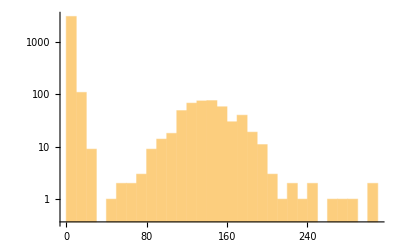

```mathematica
Histogram[Flatten@Table[
cellArea[#,t]&/@cellsRemovedTS[[t]],
{t,Length@cellsRemovedTS}
],
{10},
PlotRange->All,
ScalingFunctions->"Log"
]
```

We see a clear separation at ca. 35, distinguishing between invaginating cells and dividing cells (the latter grow in area before dividing). We use this threshold to identify all invaginating cells as those with an area below 35 before they disappear.

```mathematica
invagSizeThreshold=35;
```

```mathematica
invagTS=Table[
Select[cellsRemovedTS[[t]],cellArea[#,t]<invagSizeThreshold&],
{t,Length@cellsRemovedTS}
];
```

```mathematica
invaginatingCells=Union[Catenate[invagTS]];
```

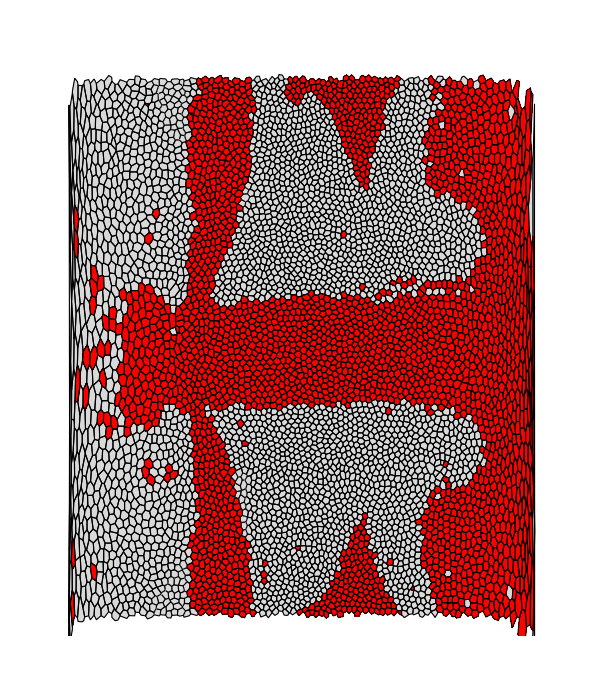

```mathematica
Graphics[{
EdgeForm[Black],FaceForm[LightGray],
renderCell2D[#,1]&/@Complement[Keys[cellCentroidsTS[[1]]],invaginatingCells],
FaceForm[Red],
Function[{c},If[#=!=Null,Tooltip[#,c]]&@renderCell2D[c,1]]/@invaginatingCells
},
PlotRange->{{0,510},{-15,570}},
ImageSize->600
]
```

Pick isolated invaginating cells by hand (only for body cells!)

```mathematica
isolatedInvaginatingCells={13978,14767,12249,12311,19243,7096,6516,6503,6490,8669,9055};
```

Invagination times color coded

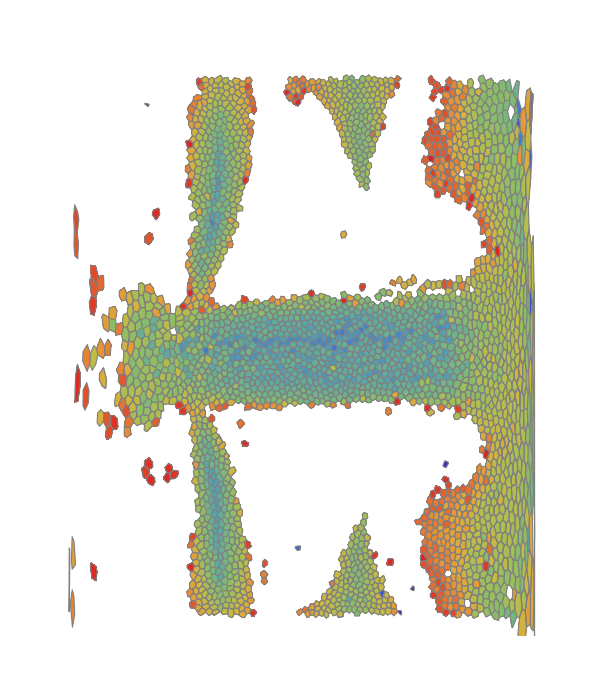

```mathematica
Graphics[{
EdgeForm[Gray],
Table[{
FaceForm[ColorData["Rainbow"][t/198.]],
renderCell2D[#,1]&/@invagTS[[t]]
},
{t,197}]
},
PlotRange->{{0,510},{-15,570}},
ImageSize->600
]
```

#### Dividing cells

```mathematica
newCells[t_]:=Complement[Keys[cellVerticesTS[[t]]],Keys[cellVerticesTS[[t-1]]]]
```

```mathematica
divTS=MapThread[Complement[#1,#2]&,{cellsRemovedTS,invagTS}];
```

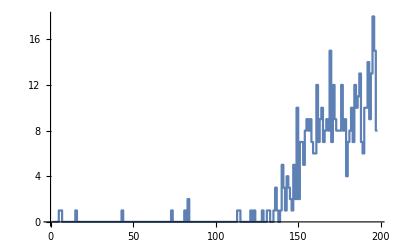

```mathematica
ListStepPlot[Length/@divTS]
```

Animation of cells disappearing and reappearing

```mathematica
Manipulate[Graphics[{
Gray,Point[toCylinder/@Values[cellCentroidsTS[[t]]]],
AbsolutePointSize[10],
Red,Point[toCylinder[#]&/@cellCentroidsTS[[t]]/@divTS[[t]]],
Darker@Green,Point[toCylinder[#]&/@cellCentroidsTS[[t+1]]/@newCells[t+1]]
},ImageSize->700],
{t,1,Length[cellCentroidsTS]-1,1}
]
```

New cell size distribution

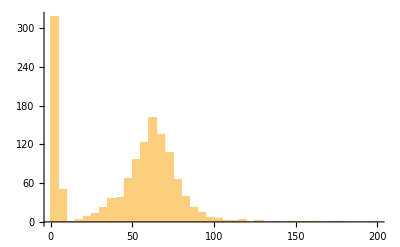

```mathematica
Histogram[Flatten[Table[cellArea[#,t]&/@newCells[t],{t,2,Length[cellCentroidsTS]}]],{5}]
```

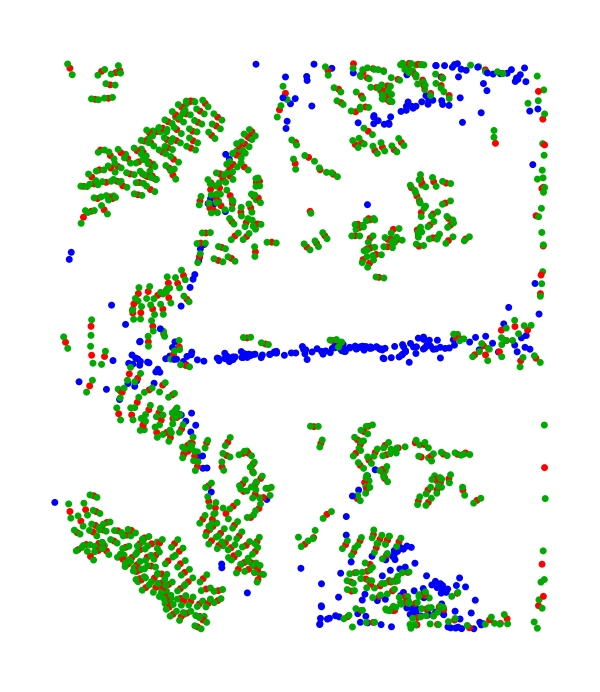

```mathematica
Graphics[Table[{
AbsolutePointSize[5],
Red,Point[toCylinder[#]&/@cellCentroidsTS[[t]]/@divTS[[t]]],
Darker@Green,Point[toCylinder[#]&/@cellCentroidsTS[[t+1]]/@Select[newCells[t+1],cellArea[#,t+1]>15.&]],
Blue,Point[toCylinder[#]&/@cellCentroidsTS[[t+1]]/@Select[newCells[t+1],cellArea[#,t+1]<15.&]]
},
{t,1,Length[cellCentroidsTS]-1,1}
],ImageSize->600]
```

```mathematica
matchDivisionEvents[1,_]={};
matchDivisionEvents[t_Integer,range_]:=Block[{
new=newCells[t],
prevCentroids=cellCentroidsTS[[t-1]],
centroids=cellCentroidsTS[[t]],
pos,
daughters
},
If[#==={},{},First[#]]&@Last@Reap[Do[
pos=prevCentroids[r];
daughters=Select[new,Norm[centroids[#]-pos]<range&];
Sow[r->daughters],
{r,divTS[[t-1]]}
]]
]
```

```mathematica
divDaughterTS=Table[matchDivisionEvents[t,10],{t,Length[cellCentroidsTS]}];
```

```mathematica
MinMax[Length[#[[2]]]&/@#&/@divDaughterTS]
```

{0,3}

Exceptions. Cell 7255 disappears in one frame (tp 128)

```mathematica
Position[Length[#[[2]]]&/@#&/@divDaughterTS,0]
```

{{138,1}}

```mathematica
divDaughterTS[[138]]
```

{7255→{}}

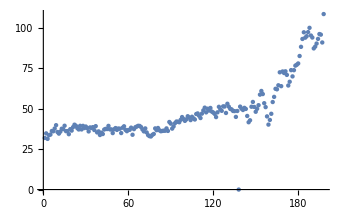

```mathematica
ListPlot[Table[cellArea[7255,t],{t,Length[cellCentroidsTS]}]]
```

There are also some daughter cells that are assigned to two progenitor cells by the simple distance-based algorithm above.

```mathematica
MinMax[Counts[Flatten[Last[#]&/@#&/@divDaughterTS]]]
```

{1,2}

```mathematica
Position[Counts[Flatten[Last[#]&/@#&/@divDaughterTS]],2]
```

{{Key[20278]},{Key[20316]},{Key[20393]},{Key[20394]},{Key[20408]},{Key[20426]},{Key[20429]},{Key[20430]},{Key[20433]},{Key[20477]},{Key[20478]},{Key[20486]},{Key[20544]},{Key[20777]},{Key[20953]},{Key[21011]},{Key[21019]},{Key[21044]},{Key[21105]},{Key[21106]}}

```mathematica
daughterCells=Union[Flatten[Last[#]&/@#&/@divDaughterTS]];
```

```mathematica
Intersection[daughterCells,Keys[cellCentroidsTS[[1]]]]
```

{}

Some cells actually divide multiple times

```mathematica
findLineage[cell_]:=TimeConstrained[Most@NestWhileList[#/.Flatten[divDaughterTS]&,cell,UnsameQ[##]&,2],1]
```

```mathematica
findLineage[18931]
```

{18931,{20166,20167},{{20172,20173},20167}}

```mathematica
offspringAssoc=Association[#->Union[Flatten[Rest@findLineage[#]]]&/@Keys[Flatten[divDaughterTS]]];
```

#### Connected components

```mathematica
headCells=Complement[Keys@Select[cellCentroidsTS[[1]],#[[1]]<150&],invaginatingCells,{3288}];
```

```mathematica
initGraph=makeGraph[Keys[cellNeighborsTS[[1]]],cellNeighborsTS[[1]]];
```

```mathematica
graphComponents=ConnectedComponents[VertexDelete[initGraph,Intersection[VertexList[initGraph],Complement[invaginatingCells,isolatedInvaginatingCells]]]];
```

```mathematica
Length/@graphComponents
```

{2423,875,3,3,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
bodyCells=graphComponents[[1]];
```

```mathematica
bodyDaughterCells=Union[Flatten[Values[KeySelect[offspringAssoc,MemberQ[bodyCells,#]&]]]];
```

```mathematica
bodyCellsLeft=Select[bodyCells,cellCentroidsTS[[1]][#][[3]]<$axisOffset[[3]]&];
bodyCellsRight=Complement[bodyCells,bodyCellsLeft];
```

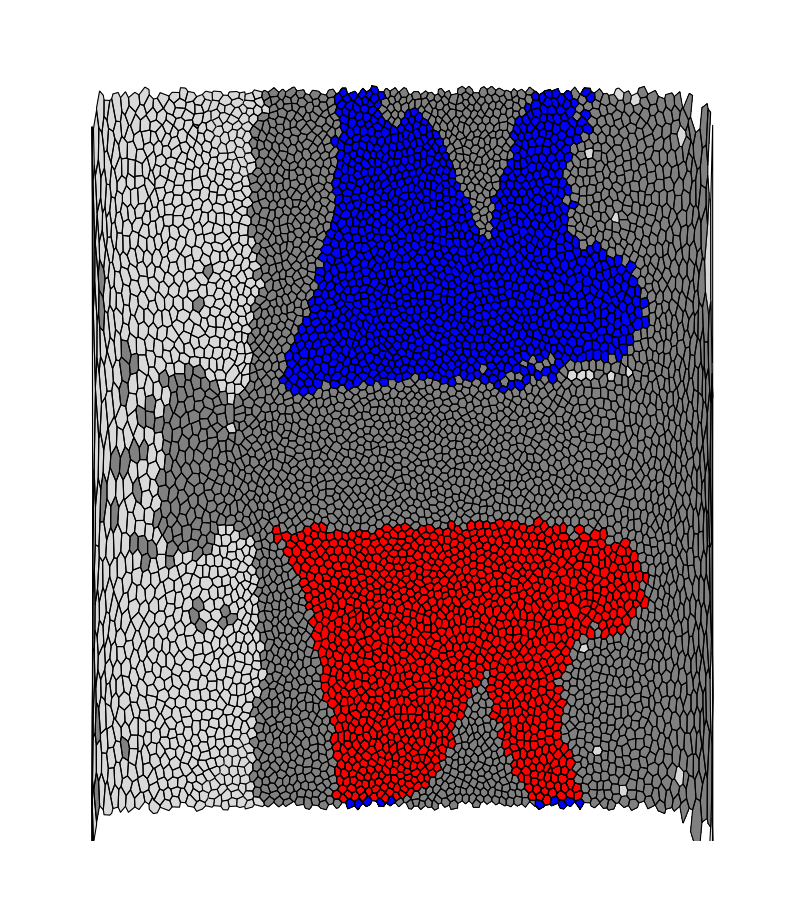

```mathematica
Graphics[{
EdgeForm[Black],FaceForm[LightGray],
renderCell2D[#,1]&/@Complement[Keys[cellCentroidsTS[[1]]],invaginatingCells],
FaceForm[Gray],
renderCell2D[#,1]&/@invaginatingCells,
FaceForm[Red],
renderCell2D[#,1]&/@bodyCellsLeft,
FaceForm[Blue],
renderCell2D[#,1]&/@bodyCellsRight
},
PlotRange->{{0,510},{-20,560}},
ImageSize->800
]
```

Dorsal body cells

```mathematica
bodyCellsDorsal=Keys[Select[KeySelect[cellCentroidsTS[[1]],MemberQ[bodyCells,#]&],$axisOffset[[3]]-15<#[[3]]<$axisOffset[[3]]+35&&#[[2]]<$axisOffset[[2]]&]];
```

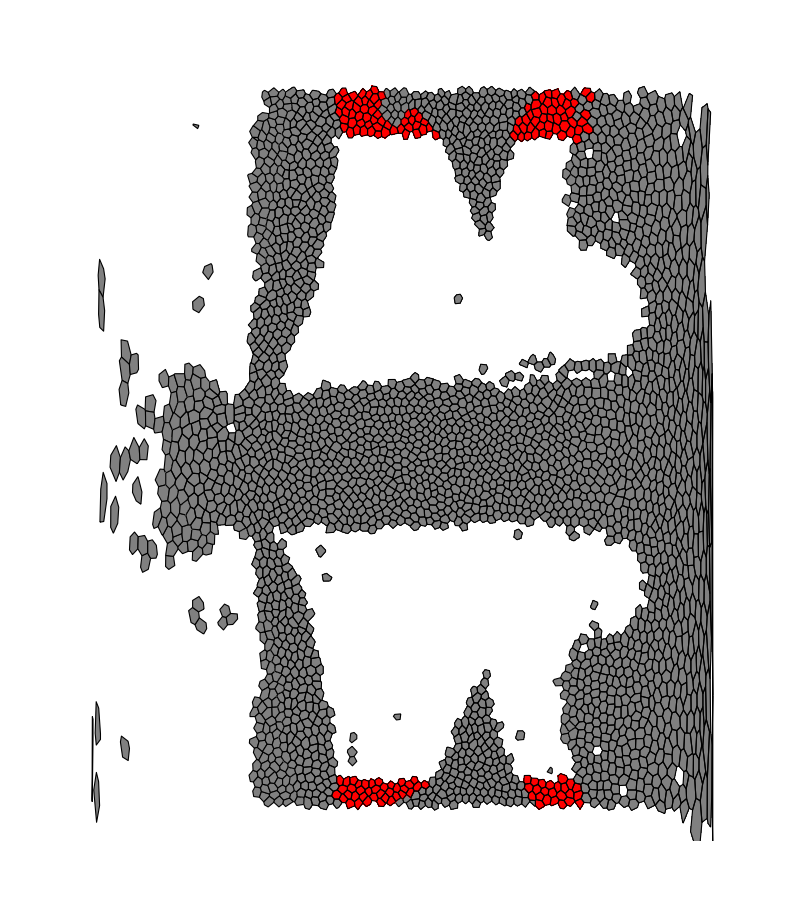

```mathematica
Graphics[{
EdgeForm[Black],FaceForm[Gray],
renderCell2D[#,1]&/@invaginatingCells,
FaceForm[Red],
renderCell2D[#,1]&/@bodyCellsDorsal
},
PlotRange->{{0,510},{-20,560}},
ImageSize->800
]
```

Cells that end up above the vertical midplane

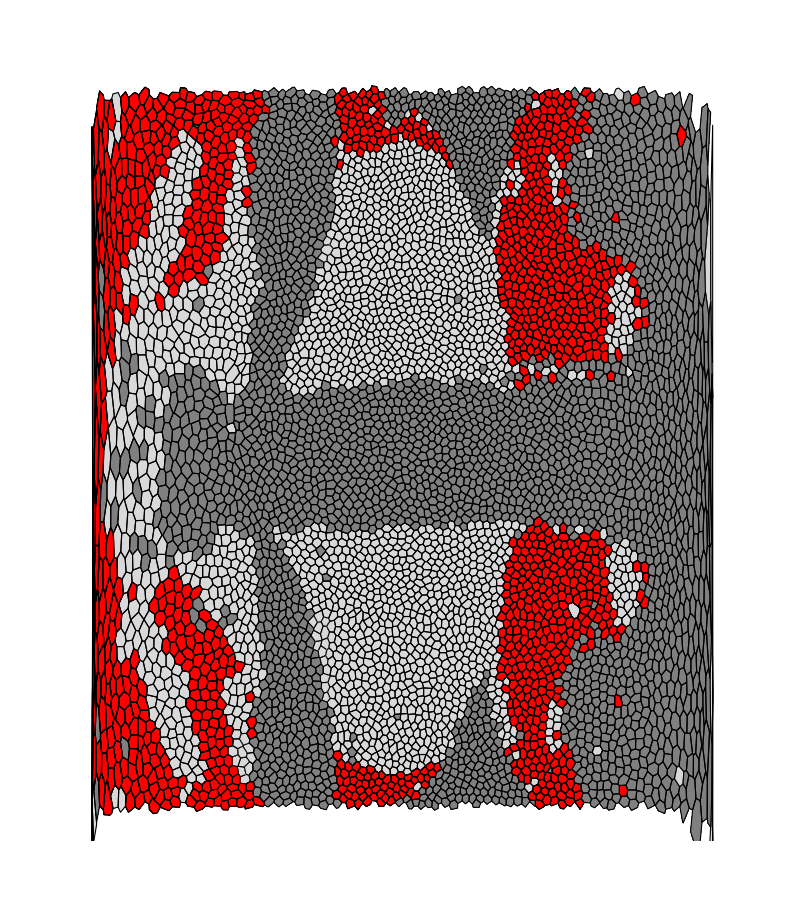

```mathematica
Graphics[{
EdgeForm[Black],FaceForm[LightGray],
renderCell2D[#,1]&/@Complement[Keys[cellCentroidsTS[[1]]],invaginatingCells],
FaceForm[Gray],
renderCell2D[#,1]&/@invaginatingCells,
FaceForm[Red],
renderCell2D[#,1]&/@Keys[Select[cellCentroidsTS[[-1]],#[[2]]<$axisOffset[[2]]&]]
},
PlotRange->{{0,510},{-20,560}},
ImageSize->800
]
```

The tip of the dorsal fold (wedge-shaped regions of invaginating cells) approximately spearates the part of the germ band that remain on the ventral side of the embryo vs those that go to the dorsal side.

We distinguish the anterior (“front”) and posterior (“back”) part of the germ band based on this criterion.

```mathematica
bodyCellsFront=Select[bodyCells,cellCentroidsTS[[1]][#][[1]]<325&];
bodyCellsBack=Complement[bodyCells,bodyCellsFront];
```

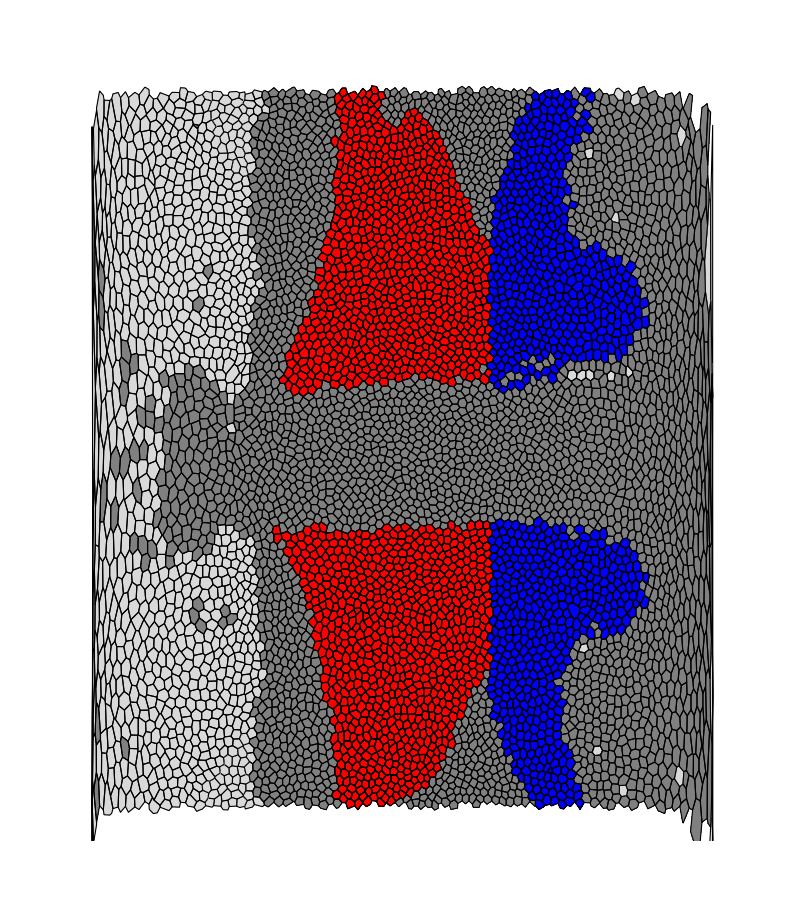

```mathematica
Graphics[{
EdgeForm[Black],FaceForm[LightGray],
renderCell2D[#,1]&/@Complement[Keys[cellCentroidsTS[[1]]],invaginatingCells],
FaceForm[Gray],
renderCell2D[#,1]&/@invaginatingCells,
FaceForm[Red],
renderCell2D[#,1]&/@bodyCellsFront,
FaceForm[Blue],
renderCell2D[#,1]&/@bodyCellsBack
},
PlotRange->{{0,510},{-20,560}},
ImageSize->800
]
```

#### Save pre-processed mesh data

```mathematica
DumpSave[dataDir<>"mesh-data.mx",{$axisOffset,$radius,vertexCoordsTS,cellCentroidsTS,cellVerticesTS,vertexCellsTS,cellNeighborsTS,
edgeVerticesTS,vertexNeighborsTS,
persistentCells,allCells,
invaginatingCells,isolatedInvaginatingCells,
bodyCells,bodyDaughterCells,bodyCellsBack,bodyCellsFront,bodyCellsLeft,bodyCellsRight,bodyCellsDorsal
}];
```

#### Ellipsoid tangential basis vectors

The surface of the embyro is approximately ellipsoidal. We use this to define a local coordinate frame that is approximately tangential to the surface.

```mathematica
Module[{
minMax=MinMax[vertexCoordsTS[[All,All,1]]],
length,center
},
{length,center}={#[[2]]-#[[1]],Mean[#]}&@minMax;
$ellipsoidCenter=Join[{center},$axisOffset[[2;;3]]];
$ellipsoidHalfLength=length/2;
$ellipsoidRadius=90;
]
ellipsoidBasis[p_]:=Module[{
x=p[[1]]-$ellipsoidCenter[[1]],ϕ=ArcTan@@(p[[2;;3]]-$ellipsoidCenter[[2;;3]]),
nr,n,eϕ
},
nr=√(1-x^2/($ellipsoidHalfLength)^2)/$ellipsoidRadius;
n=Normalize@{x/($ellipsoidHalfLength)^2,Cos[ϕ]nr,Sin[ϕ]nr};
eϕ={0,-Sin[ϕ],Cos[ϕ]};
{
Cross[n,eϕ],
eϕ,
n
}
]
```

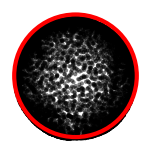

```mathematica
Graphics[{
Opacity[0.5],
Point[Transpose[{1,-1}Transpose[vertexCoordsTS[[-1,All,{3,2}]]]]],
Opacity[1],Red,AbsoluteThickness[3],
Circle[{1,-1}$ellipsoidCenter[[{3,2}]],{$ellipsoidRadius,$ellipsoidRadius}]
},
ImageSize->150
]
```

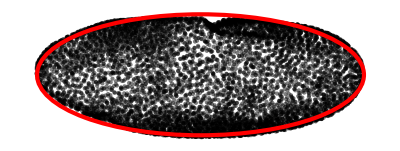

```mathematica
Graphics[{
Opacity[0.5],
Point[Transpose[{1,-1}Transpose[vertexCoordsTS[[-1,All,1;;2]]]]],
Opacity[1],Red,AbsoluteThickness[3],
Circle[{1,-1}$ellipsoidCenter[[1;;2]],{$ellipsoidHalfLength,$ellipsoidRadius}]
}]
```

Distance along midline approximating the crosssection as an ellipsoid.

l=a((∫_ϕ)_0)^ϕ_1 dϕ x √(1-(1-b^2/a^2) sin(ϕ))

```mathematica
midlineDistance[ϕ0_,ϕ1_]:=With[{e2=1-($ellipsoidRadius)^2/($ellipsoidHalfLength)^2},
$ellipsoidHalfLength(EllipticE[ϕ1,e2]-EllipticE[ϕ0,e2])]
```

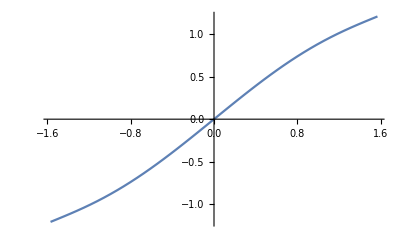

```mathematica
Plot[EllipticE[ϕ,3/4],{ϕ,-π/2,π/2},PlotRange->All]
```

```mathematica
midlineDistance[-π/2,π/2]
```

549.665

```mathematica
Perimeter[Disk[{0,0},{$ellipsoidRadius,$ellipsoidHalfLength}]]/2
```

549.665

```mathematica
midlineAngle[x_,y_]:=ArcTan[x-$ellipsoidCenter[[1]],y-$ellipsoidCenter[[2]]]
```

```mathematica
Manipulate[
Column[{
{midlineAngle@@p,midlineDistance[0,midlineAngle@@p]},
Graphics[{
Circle[$ellipsoidCenter[[1;;2]],{$ellipsoidHalfLength,$ellipsoidRadius}],
Point[p],
Line[{$ellipsoidCenter[[1;;2]],p}]
},
ImageSize->400
]
}],
{{p,$ellipsoidCenter[[1;;2]]+{0,$ellipsoidRadius}},Locator}
]
```

#### Advected (“Lagrangian”) basis vectors

Pre-compute for all cells and all timepoints

```mathematica
(* This runs for ca 1h30min *)
advectedCellBasisTS=Table[
Association[#->transportLocalBasis[#,1,t]&/@Intersection[bodyCells,Keys[cellCentroidsTS[[1]]],Keys[cellCentroidsTS[[t]]]]],
{t,198}
];//AbsoluteTiming
```

{5226.9,Null}

```mathematica
Export[dataDir<>"advectedCellBasisTS.mx",advectedCellBasisTS];
```

Rending: initial timepoint

```mathematica
localBases=transportLocalBasis[#,1,2]&/@sampleCellsSparse[2,5,Complement[Keys[cellCentroidsTS[[2]]],Keys[cellCentroidsTS[[1]]]]];
```

```mathematica
With[{t=2},
Graphics3D[{
AbsoluteThickness[2.5],
RGBColor[0.9,0,0],
Line[{#[[2]]+2#[[3,3]],#[[2]]+2#[[3,3]]-10#[[3,2]]}]&/@localBases,
RGBColor[0,0,1],
Line[{#[[2]]+2#[[3,3]],#[[2]]+2#[[3,3]]+10#[[3,1]]}]&/@localBases,
EdgeForm[None],AmbientLight[GrayLevel[0.8]],DirectionalLight[GrayLevel[0.4],{10,-20,10}],
GraphicsComplex[
vertexCoordsTS[[t]],{
GrayLevel[0.8],Polygon[cellVerticesTS[[t]][#]]&/@Complement[Keys[cellCentroidsTS[[t]]],Catenate[zoneCells[[1;;2]]],invaginatingCells],
GrayLevel[0.6],Polygon[cellVerticesTS[[t]][#]]&/@Intersection[invaginatingCells,Keys[cellCentroidsTS[[t]]]],
zoneColors[[2]],
Polygon[cellVerticesTS[[t]][#]]&/@Intersection[Catenate[zoneCells[[1;;2]]],Keys[cellCentroidsTS[[t]]]]
}
]
},
Boxed->False,Lighting->None,
ViewPoint->{80, -15,-100},ViewVertical->{0,-1,0},
Background->White,ImageSize->400
]]
```

-Graphics3D-

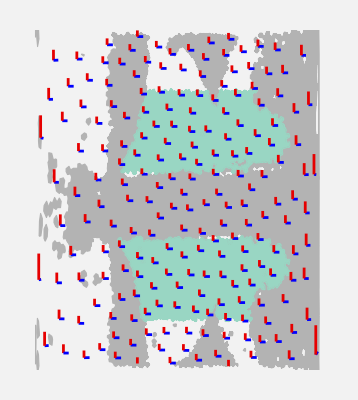

```mathematica
Graphics[{
EdgeForm[GrayLevel[0.7]],FaceForm[GrayLevel[0.7]],
renderCellGroup2D[invaginatingCells,1],
EdgeForm[Lighter@zoneColors[[2]]],FaceForm[Lighter@zoneColors[[2]]],
renderCellGroup2D[Catenate[zoneCells[[1;;2]]],1],
AbsoluteThickness[2],
{
RGBColor[0,0,1],
Line[toCylinder[{#[[2]],#[[2]]+10#[[3,1]]}]],
RGBColor[0.9,0,0],
Line[toCylinder[{#[[2]],#[[2]]+10#[[3,2]]}]],
If[periodicBoundaryQ[{#[[2]],#[[2]]+10#[[3,2]]}],
Line[toCylinder[{#[[2]],#[[2]]+10#[[3,2]]},Offset->π]]
]
}&/@localBases
},
PlotRange->{{10,510},{0,2π $radius}},
Background->GrayLevel[0.95]
]
```

Rendering: late timepoint (35 min)

```mathematica
localBases=transportLocalBasis[#,1,140]&/@sampleCellsSparse[140,4,Complement[Keys[cellCentroidsTS[[140]]],Keys[cellCentroidsTS[[1]]]]];
```

```mathematica
With[{t=140},
Graphics3D[{
AbsoluteThickness[2.5],
RGBColor[0.9,0,0],
Line[{#[[2]]+2#[[3,3]],#[[2]]+2#[[3,3]]-10#[[3,2]]}]&/@localBases,
RGBColor[0,0,1],
Line[{#[[2]]+2#[[3,3]],#[[2]]+2#[[3,3]]+10#[[3,1]]}]&/@localBases,
EdgeForm[None],AmbientLight[GrayLevel[0.8]],DirectionalLight[GrayLevel[0.4],{10,-20,10}],
GraphicsComplex[
vertexCoordsTS[[t]],{
GrayLevel[0.8],Polygon[cellVerticesTS[[t]][#]]&/@Complement[Keys[cellCentroidsTS[[t]]],Catenate[zoneCells[[1;;2]]],invaginatingCells],
GrayLevel[0.6],Polygon[cellVerticesTS[[t]][#]]&/@Intersection[invaginatingCells,Keys[cellCentroidsTS[[t]]]],
zoneColors[[2]],
Polygon[cellVerticesTS[[t]][#]]&/@Intersection[Catenate[zoneCells[[1;;2]]],Keys[cellCentroidsTS[[t]]]]
}
]
},
Boxed->False,Lighting->None,
ViewPoint->{80, -15,-100},ViewVertical->{0,-1,0},
Background->White,ImageSize->400
]]
```

-Graphics3D-

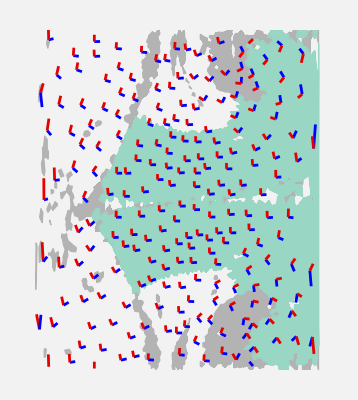

```mathematica
Graphics[{
EdgeForm[GrayLevel[0.7]],FaceForm[GrayLevel[0.7]],
renderCellGroup2D[invaginatingCells,140],
EdgeForm[Lighter@zoneColors[[2]]],FaceForm[Lighter@zoneColors[[2]]],
renderCellGroup2D[Catenate[zoneCells[[1;;2]]],140],
AbsoluteThickness[2],
{
RGBColor[0,0,1],
Line[toCylinder[{#[[2]],#[[2]]+10#[[3,1]]}]],
RGBColor[0.9,0,0],
Line[toCylinder[{#[[2]],#[[2]]+10#[[3,2]]}]],
If[periodicBoundaryQ[{#[[2]],#[[2]]+10#[[3,2]]}],
Line[toCylinder[{#[[2]],#[[2]]+10#[[3,2]]},Offset->π]]
]
}&/@localBases
},
PlotRange->{{10,510},{0,2π $radius}},
Background->GrayLevel[0.95]
]
```